```mathematica
ClearAll["Global`*"];
(* Hamulce twojego samochodu są zdolne hamować pojazd z przyspieszeniem równym ah=5.2m*s^2. Jeżeli jedziesz z prędkością vp=137 km/h i nagle spostrzegasz patrol policji,to w jakim czasie jeste±w staniezwolnic do dopuszczalnej prędkości vd =90km/h?Sporządź wykres x(t) i v(t) w czasie hamowania samochodu. *)
```

```mathematica
ah=5.2 (* m/s^2 *)
```

5.2

```mathematica
vp=137×1000/3600  //N (* m/s *)
```

38.0556

```mathematica
vd=90×1000/3600  //N (* m/s *)
```

25.

```mathematica
rown1=Solve[vd==vp-ah ×th,th]
```

{{th→2.51068}}

```mathematica
tk=th/. rown1[[1,1]]
```

2.51068

```mathematica
x= vp ×t - (ah×t^2)/2
v=vp-ah ×t
```

38.0556 t-2.6 t^2

38.0556-5.2 t

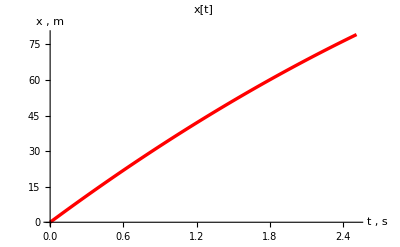

```mathematica
rysxt=Plot[x,{t,0,tk},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->"x[t]",PlotStyle->{RGBColor[1,0,0],Thickness[0.006]},AxesLabel->{"t , s","x , m "}]
```

### Sporządzenie wykresu zależności prędkości “v” od czasu “t”.

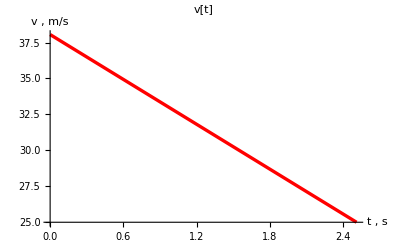

```mathematica
rysvt=Plot[v,{t,0,tk},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->"v[t]",PlotStyle->{RGBColor[1,0,0],Thickness[0.006]},AxesLabel->{"t , s","v , m/s "}]
```